```mathematica
Quit[];
```

```mathematica
(*TBP Induction Data*)
inductionData = {{0,0}, {10, 0}, {20,0.0668815}, {25, 0.1881925}, {30, 0.3927595}, {40,0.702039}, {60,0.93478}, {90,1.0869705},{120,1.0}};
```

```mathematica
inductionFit=NonlinearModelFit[inductionData,X*((t/t0)^4/((t/t0)^4+1)),{X,t0},t];
```

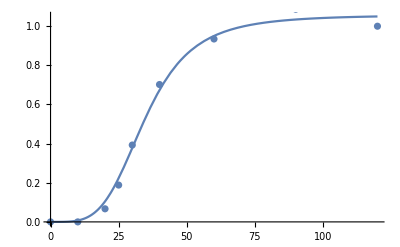

```mathematica
Show[{Plot[Normal[inductionFit[t]],{t,0,120}],ListPlot[inductionData]}]
```

```mathematica
%3["ParameterTable"]
```

(-Graphics-)[ParameterTable]

```mathematica
%2
```

FittedModel[(7.25756×10^-7 t^4)/(1+6.86451×10^-7 t^4)]

```mathematica
%2["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
X | 1.05726 | 0.0236333 | 44.736 | 7.28549×10^-10
t0 | 34.7414 | 0.913918 | 38.0137 | 2.2681×10^-9

```mathematica
time = {10,20,25,30,40,60,90,120};
```

```mathematica
{10,20,25,30,40,60,90,120}
```

{10,20,25,30,40,60,90,120}

```mathematica
ratioData = Import["/Users/sb3de/Box Sync/stefan/projects/TF-Chromatin_Dynamics/Competition_ChIP_Bekiranov/competition_ChIP/TBP/Normalized_Ratio_Data/tbp_ratioCountTable_readDepth_and_western_normalized_no_head.txt","Table"];
```

```mathematica
Sites=Length[ratioData];
```

```mathematica
cBSat=inductionFit["BestFitParameters"][[1]][[2]];
```

```mathematica
t0=inductionFit["BestFitParameters"][[2]][[2]];
```

```mathematica
cB[t_]=cBSat*((t/t0)^4/((t/t0)^4+1));
```

```mathematica
modela=ParametricNDSolveValue[{b'[t]==-kd*b[t]+ka*cB[t]*(1-a[t]-b[t]),a'[t]==-kd*a[t]+ka*(1-a[t]-b[t]),a[0]==ka/(ka+kd),b[0]==0},a,{t,0,120},{ka,kd}];
```

```mathematica
modelb=ParametricNDSolveValue[{b'[t]==-kd*b[t]+ka*cB[t]*(1-a[t]-b[t]),a'[t]==-kd*a[t]+ka*(1-a[t]-b[t]),a[0]==ka/(ka+kd),b[0]==0},b,{t,0,120},{ka,kd}];
```

```mathematica
inductionModel[X_,t1_,t_]=X*((t/t1)^4/((t/t1)^4+1));
```

```mathematica
TestList ={};
```

```mathematica
AppendTo[TestList,{"Site","t1 [min]","t1_Error [min]","t1_p-value","Hill_Model_RSquared","t1/2 [min]","kd [1/min]","kd_Error [1/min]","kd_p-value","Turnover_Model_RSquared"}];
```

```mathematica
For[i=1,i≤Sites,i++, 
ratioDataTemp = ratioData[[i,2;;9]]; 
dataToFitPreScaled={time,ratioDataTemp}//Transpose;inductionFitToData = NonlinearModelFit[dataToFitPreScaled, {inductionModel[X,t1,t]+B,X>0,t1>0,B>0},{{X,ratioDataTemp[[8]]-ratioDataTemp[[1]]},{t1,36.7},{B,ratioDataTemp[[1]]}},t,MaxIterations->100]; ampTemp=inductionFitToData["BestFitParameters"][[1]][[2]];t1Temp=inductionFitToData["BestFitParameters"][[2]][[2]];backTemp=inductionFitToData["BestFitParameters"][[3]][[2]];ratioDataBackSubTemp = ratioDataTemp - backTemp;scaleFactor = cBSat/ampTemp;dataToFitTemp={time,scaleFactor*ratioDataBackSubTemp}//Transpose;t1ErrorTemp=inductionFitToData["ParameterErrors"][[2]];t1Pvalue=inductionFitToData["ParameterPValues"][[2]];t1RSquared =inductionFitToData["RSquared"];If[t1Temp>t0 &&t1RSquared>0.7 && ampTemp > 0,
resTimeInit =0.608*(t1Temp-t0)+0.082;
kdEst = Log[2]/resTimeInit;
kaEst=kdEst;turnoverModel=NonlinearModelFit[dataToFitTemp,modelb[ka,kd][t]/modela[ka,kd][t],{{ka,kaEst},{kd,kdEst}},t,MaxIterations->100];kdTemp=turnoverModel["BestFitParameters"][[2]][[2]];resTimeTemp=Log[2]/kdTemp;kdErrorTemp=turnoverModel["ParameterErrors"][[2]];kdPvalueTemp=turnoverModel["ParameterPValues"][[2]];kdRSquared=turnoverModel["RSquared"];AppendTo[TestList,{ratioData[[i,1]],t1Temp,t1ErrorTemp,t1Pvalue,t1RSquared,resTimeTemp,kdTemp,kdErrorTemp,kdPvalueTemp,kdRSquared}]; ,AppendTo[TestList,{ratioData[[i,1]],t1Temp,t1ErrorTemp,t1Pvalue,t1RSquared,"NA","NA","NA","NA","NA"}];];];
```

```mathematica
Export["/Users/sb3de/test/TBP_Turnover_Model_RD_Western_Norm_RSqr70Pct_Medt1_Exact_Init.tsv",TestList];
```